```mathematica
data1=Import["collapse_data_10x5.m"];
data2=Import["collapse_data_20x10.m"];
data3=Import["collapse_data_40x20.m"];
data4=Import["collapse_data_80x40.m"];
data={data1,data2,data3,data4};
```

```mathematica
dist={};plots={};stats={};
For[i=1,i≤Length[data],i++,
(*data[[i]]=Round[data[[i]],0.1];*)
(*data[[i]]=data[[i]]-Mean[data[[i]]];*)
AppendTo[dist,EmpiricalDistribution[data[[i]]]];
plotPDF=DiscretePlot[PDF[dist[[i]],x],{x,data[[i]]},PlotLabel->Text[TraditionalForm["PDF(H)"]]];
plotCDF=DiscretePlot[CDF[dist[[i]],x],{x,Min[data[[i]]],Max[data[[i]]],.01},PlotLabel->Text[TraditionalForm["P_f(H)"]]];
AppendTo[plots,{plotPDF,plotCDF}];
AppendTo[stats,{Mean[dist[[i]]],Quantile[dist[[i]],0.05],StandardDeviation[dist[[i]]],StandardDeviation[dist[[i]]]/Mean[dist[[i]]]}]
];
```

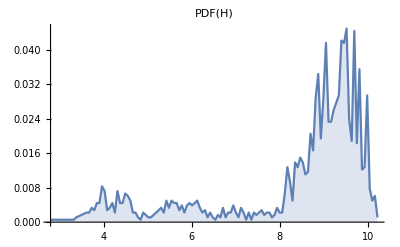
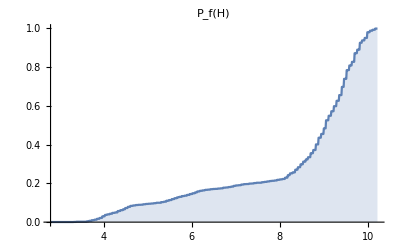
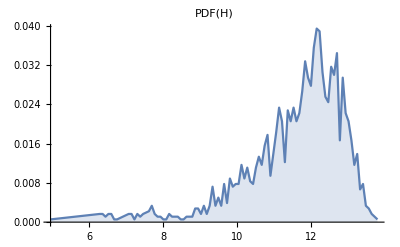
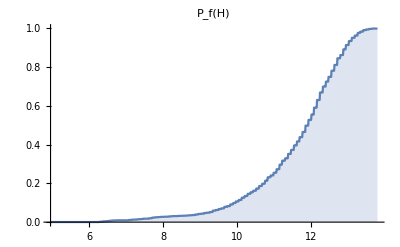
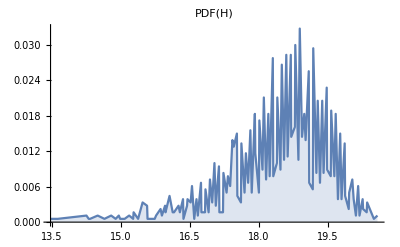
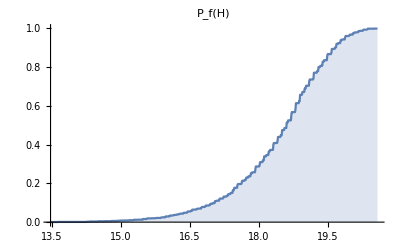
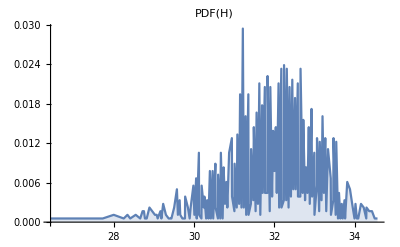
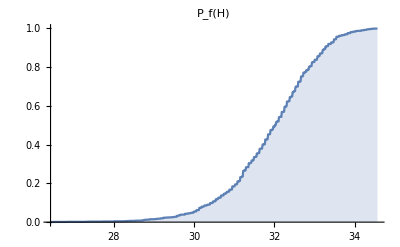

{{8.39121,4.24805,1.7337,0.206609},{11.5856,9.25781,1.29191,0.111509},{18.4276,16.4453,1.06401,0.0577402},{31.9081,29.9854,1.13467,0.0355606}}

```mathematica
plots
stats
```

```mathematica
Export["risultati_collasso_1.pdf",GraphicsGrid[plots[[1;;1]]],ImageSize->500,ImageResolution->200]
```

risultati_collasso_1.pdf

```mathematica
Export["risultati_collasso_2.pdf",GraphicsGrid[plots[[2;;2]]],ImageSize->500,ImageResolution->200]
```

risultati_collasso_2.pdf

```mathematica
Export["risultati_collasso_3.pdf",GraphicsGrid[plots[[3;;3]]],ImageSize->500,ImageResolution->200]
```

risultati_collasso_3.pdf